```mathematica
ClearAll["Global`*"]
```

Copy here the epxressions used in openQCDrad.
These correspond to Fig.6 in [Laenen, Riemersma, Smith: “Complete O(<i>α</i>S) corrections to heavy-flavour structure functions in electroproduction”, Nucl. Phys. B, 392 (1), 162-228, 1993].

(π (-2 √(η/(1+η)) (1+η+(1+η-ξ/4)^2)+(1+2 η+2 (1+η)^2+ξ^2/8) Log[(√η+√(1+η))/(-√η+√(1+η))]))/(4 (1+η+ξ/4)^3)

(π ξ (2 √(η (1+η))-Log[(√η+√(1+η))/(-√η+√(1+η))]))/(4 (1+η+ξ/4)^3)

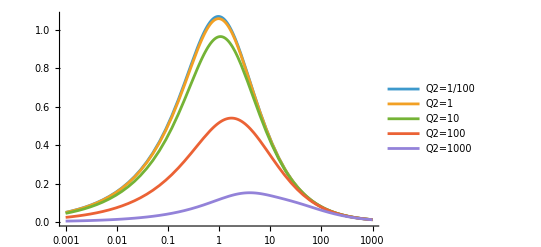

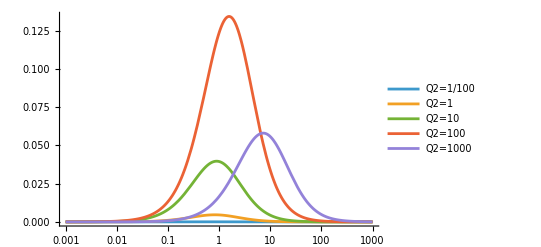

```mathematica
ξ[Q_,m_]:=Q^2/m^2;
η[s_,m_]:=s/(4*m^2)-1;
TR=1/2;
ctgoqcdr[η_,ξ_]:=π/2*TR*(1+η+ξ/4)^(-3)*(-2*((1+η-ξ/4)^2+η+1)*Sqrt[η/(1+η)]+(2*(1+η)^2+ξ^2/8+2*η+1)*Log[(Sqrt[1+η]+Sqrt[η])/(Sqrt[1+η]-Sqrt[η])])
clgoqcdr[η_,ξ_]:=π/2*TR*ξ*(1+η+ξ/4)^(-3)*(2*Sqrt[η*(1+η)]-Log[(Sqrt[1+η]+Sqrt[η])/(Sqrt[1+η]-Sqrt[η])])

DisplayForm[ctgoqcdr[η,ξ]]
DisplayForm[clgoqcdr[η,ξ]]

Q2vals={10^-2,1,10,100,1000};
LogLinearPlot[Evaluate@ctgoqcdr[η,ξ[Sqrt@Q2vals,4.75]],{η,0.001,1000},AxesStyle->{Log},PlotLegends->Map[Row[{"Q2=",DisplayForm[#]}]&,Q2vals]]
LogLinearPlot[Evaluate@clgoqcdr[η,ξ[Sqrt@Q2vals,4.75]],{η,0.001,1000},AxesStyle->{Log},PlotLegends->Map[Row[{"Q2=",DisplayForm[#]}]&,Q2vals],PlotRange->Full]
```

Let’s see if we can reconstruct these from the information of said paper, because it is not immediately clear...

```mathematica
rules={
rs->(1-sb)/(1+sb),(*eq 2.18*)
sb->Sqrt[1-4*m^2/s],(*after eq. 2.18*)
sp->s-q^2,(*eq 2.4*)
q->I*m*Sqrt[ξ],
s->4*m^2*(η+1),
Kgγ->1/(N^2-1),
CF->(N^2-1)/(2N)
};

σLg=16*π*Kgγ*α*αs*eH^2*N*CF*(-q^2*s/sp^3)*(sb+2m^2/s*Log[rs])//Simplify;
σTg=4*π*Kgγ*α*αs*eH^2*N*CF*1/sp*(-((s+q^2)^2+4m^2*s)/(sp^2)*sb-((s^2+(q^2)^2)/(sp^2)+(4m^2*s)/(sp^2)-(8*m^4)/(sp^2))*Log[rs])//Simplify;

FL=-q^2/(4*π^2*α)*σLg;
F1=pq/(4*π^2*α)*σTg/.pq->-q^2/(2*x);

DisplayForm[σLg//.rules]
DisplayForm[σTg//.rules]
DisplayForm[FL//.rules//Simplify]
DisplayForm[clgoqcdr[η,ξ]/.η->η[s,m]//Simplify]
```

(8 eH^2 m^2 π α αs ξ (4 m^2 (1+η) √(1-1/(1+η))+2 m^2 Log[(1-√(1-1/(1+η)))/(1+√(1-1/(1+η)))]))/((4 m^2 (1+η)+m^2 ξ)^3)

-1/((4 m^2 (1+η)+m^2 ξ)^3)2 eH^2 π α αs (√(1-1/(1+η)) (4 m^2 (1+η) (4 m^2+4 m^2 (1+η))-8 m^4 (1+η) ξ+m^4 ξ^2)+(-8 m^4+16 m^4 (1+η)+16 m^4 (1+η)^2+m^4 ξ^2) Log[(1-√(1-1/(1+η)))/(1+√(1-1/(1+η)))])

(4 eH^2 αs ξ^2 ((2 η)/(√(η/(1+η)))+Log[-(-1+√(η/(1+η)))/(1+√(η/(1+η)))]))/(π (4+4 η+ξ)^3)

(8 m^6 π ξ (√((s (-4 m^2+s))/m^4)-2 Log[(√(s/m^2)+√(-4+s/m^2))/(√(s/m^2)-√(-4+s/m^2))]))/((s+m^2 ξ)^3)

Expressions from [Glück, Reya: “Deep inelastic quantum chromodynamic charm leptoproduction”, Phys. Lett. B, 83 (1), 98, 1979]

```mathematica
v=Sqrt[1-4*m/sh];
sh=!=Q2*(1/z-1);
flg[z_,Q2_]:=eH^2*αs/π*(2*z^2*(1-z)*v-(4*m^2/Q2)*z^3*Log[(1+v)/(1-v)]);
```

```mathematica
flg[z,Q2]
```

(eH^2 αs (2 √(1-(4 m)/sh) (1-z) z^2-(4 m^2 z^3 Log[(1+√(1-(4 m)/sh))/(1-√(1-(4 m)/sh))])/Q2))/π